```mathematica
(*
e[x]_here = e_1(x)_{Lagrangian approach};
v[x]_here = {v^1(x)}_{Lagrangian approach};
σ[x]_here  = σ(x)_{Lagrangian approach};
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ[1]=1;
```

```mathematica
ass={ψ[x]∈Reals,ν[x]>0};
```

```mathematica
e[x_]:=ν[x]{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν[x] ψ'[x]}}

```mathematica
b[x_]:={{-ν[x] ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν[x])

```mathematica
H[x_]:=-ψ'[x]/(2 ν[x])
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[x],{x}] //FullSimplify
```

```mathematica
Γ[x]
```

{{{ν'[x]/ν[x]}}}

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,1}]
```

```mathematica
(*\Nabla_k v^i*)
```

```mathematica
Nablav[v_][i_,k_][x_]:=Derivative[ϵ[k]][v[i]][x]+Sum[v[j][x] Γ[x][[i,j,k]],{j,1,1}]
```

```mathematica
(*Nabla_k t^{il}*)
```

```mathematica
Nablavv[t_][i_,l_,k_][x_]:=Derivative[ϵ[k]][t[i,l]][x]+Sum[t[j,l][x] Γ[x][[i,j,k]],{j,1,1}]+Sum[t[i,j][x] Γ[x][[l,j,k]],{j,1,1}]
```

```mathematica
dH[1][x_]:=H'[x]
```

```mathematica
(*expression for Nabla_i Nabla^i H*)
```

```mathematica
FullSimplify[Sum[gc[x][[i,j]]Nablaf[dH][i,j][x],{i,1,1},{j,1,1}],Assumptions->ass]
```

(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] ψ^(3)[x]))/(2 ν[x]^5)

```mathematica
NabNabH[x_]:=(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] Derivative[3][ψ][x]))/(2 ν[x]^5)
```

```mathematica
(*auxiliary definition to obtain the covariant derivatives of v*)
```

```mathematica
vv[1][x_]:=v[x]
```

```mathematica
FullSimplify[Nablav[vv][1,1][x],Assumptions->ass]
```

v'[x]+(v[x] ν'[x])/ν[x]

```mathematica
(*Nablaivi = Nabla_i v^i*)
```

```mathematica
Nablaivi[x_]:=FullSimplify[Nablav[vv][1,1][x],Assumptions->ass]
```

```mathematica
(*rate-of-deformation tensor d^{ij}*)
```

```mathematica
dc[1,1][x_]:=gc[x][[1,1]]Nablav[vv][1,1][x]-w[x]gc[x][[1,1]]gc[x][[1,1]]b[x][[1,1]]
```

```mathematica
eqv=FullSimplify[ρ(v[x]Nablaivi[x]-2 v[x]w[x] gc[x][[1,1]]b[x][[1,1]]-w[x] gc[x][[1,1]]w'[x])
-gc[x][[1,1]]σ'[x]-2 η Nablavv[dc][1,1,1][x]==0,Assumptions->ass];
eqσ=FullSimplify[Nablaivi[x]-2 H[x]w[x]==0,Assumptions->ass];
eqψ=FullSimplify[{ρ v[x](v[x]b[x][[1,1]]+w'[x])
-κ( - 2 NabNabH[x]-4H[x](H[x]^2-K[x]))
-2 σ[x]H[x]
- 2η( Nablaivi[x] gc[x][[1,1]]b[x][[1,1]]-2 w[x]*(2 H[x]^2-K[x]))==0},Assumptions->ass];
eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]};
```

```mathematica
eqv
```

v[x] (ρ ν[x]^4 v'[x]+2 η ν'[x]^2+ρ ν[x]^3 (v[x] ν'[x]+2 w[x] ψ'[x])-2 η ν[x] ν''[x])==ν[x] (ν[x] σ'[x]+2 η (v'[x] ν'[x]+w'[x] ψ'[x]+ν[x] v''[x]))+w[x] (ρ ν[x]^2 w'[x]-2 η ν'[x] ψ'[x]+2 η ν[x] ψ''[x])

```mathematica
(* given that I am at steady state, it must be w[x]=0, thus I simplify the equations by setting *)
```

```mathematica
w[x_]:=0
```

```mathematica
eqσ
```

ν[x] v'[x]+v[x] ν'[x]==0

```mathematica
(*
eqσ implies that ν[x] * v[x] = const., thus  

v[x]=A/ν[x];
  v[xmin]=A/ν[xmin];
  A= v[xmin] * ν[xmin];
thus
v[x]=v[xmin] * ν[xmin]/ν[x]
*)
```

```mathematica
repv={v[x]->A/ν[x],v'[x]->-(A ν'[x])/ν[x]^2,v''[x]->(A (2 ν'[x]^2-ν[x] ν''[x]))/ν[x]^3};
```

```mathematica
(*the boundary condition n_i Pi^{ij} = 0 at partial_Omega_r is automatically satisfied by the solution for v given by repv*)
```

```mathematica
dc[1,1][x]/.repv
```

0

```mathematica
FullSimplify[eqv/.repv]
```

ν[x] σ'[x]==0

```mathematica
(*eqv thus implies that σ[x]= σc*)
```

```mathematica
σ[x_]:=σc
```

```mathematica
(*we thus reduce the original problem for v,w,σ,ψ,X to a reduced problem for ψ and X only*)
```

```mathematica
(*the boundary conditions and differential equations for the reduced problem are*)
```

```mathematica
bcs={
ψ[xmin]==ψmin,ψ[xmax]==ψmax,ψ'[xmin]==ψpmin,
X1[xmin]==X1min,X2[xmin]==X2min};
```

```mathematica
eqs=Flatten[{eqψ,eqX}/.repv]
```

{2 A^2 ρ ν[x]^4 ψ'[x]+ψ'[x] (6 κ ν'[x]^2+ν[x] (ν[x] ψ'[x] ((4 A η σc ν'[x])/ν[x]+κ ψ'[x])-2 κ ν''[x]))+2 κ ν[x]^2 ψ^(3)[x]==2 ν[x] (2 A η σc ν'[x] ψ'[x]^2+3 κ ν'[x] ψ''[x]),X1'[x]==Cos[ψ[x]] ν[x],X2'[x]==-Sin[ψ[x]] ν[x]}

```mathematica
(*parameters*)
```

```mathematica
κ=1;
ρ=1;
η=1;
xmin=1;
xmax=3;
vmin=1;
A=vmin*ν[xmin];
σc=0;
ψmin=-1/2;
ψmax=2;
ψpmin=-1;
X1min=0;
X2min=0;
```

```mathematica
bcs
```

{ψ[1]==-1/2,ψ[3]==2,ψ'[1]==-1,X1[1]==0,X2[1]==0}

```mathematica
ν[x_]:=1.01
```

```mathematica
(*ν[x_]:=x/(1+x)*)
```

```mathematica
s=NDSolve[FullSimplify[Flatten[{eqs,bcs}]],{ψ,X1,X2},{x,xmin,xmax}][[1]]
```

{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}

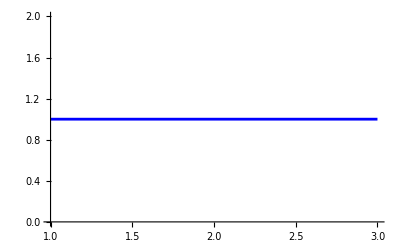

```mathematica
plotvexact=Plot[v[x]/.repv/.s,{x,xmin,xmax},PlotStyle->Blue]
```

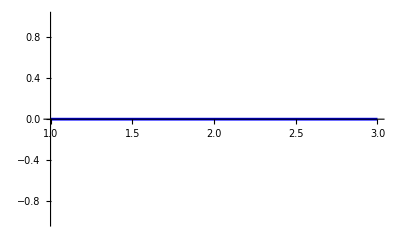

```mathematica
plotwexact=Plot[w[x],{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
plotσexact=Plot[σ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

-Graphics-

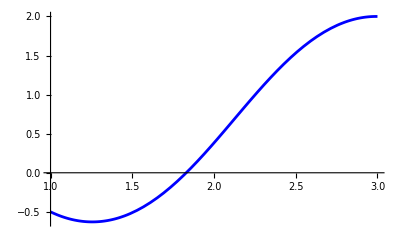

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

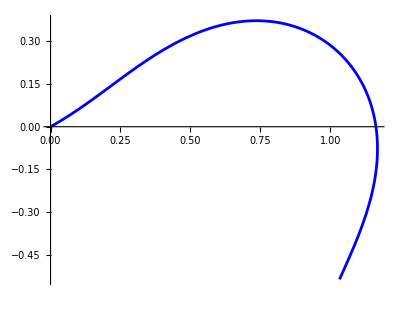

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check v*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/v.csv"];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,1.},{2.9,1.},{2.8,1.},{2.7,1.},{2.6,1.},{2.5,1.},{2.4,1.},{2.3,1.},{2.2,1.},{2.1,1.},{2.,1.},{1.9,1.},{1.8,1.},{1.7,1.},{1.6,1.},{1.5,1.},{1.4,1.},{1.3,1.},{1.2,1.},{1.1,1.},{1.,1.}}

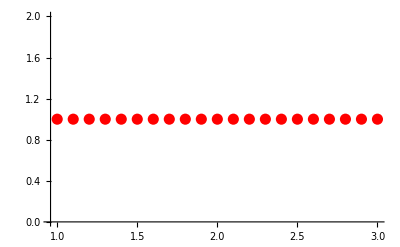

```mathematica
plotvnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

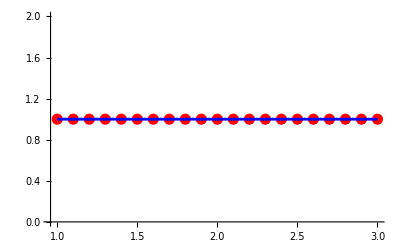

```mathematica
Show[plotvnum,plotvexact]
```

```mathematica
(*check w*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/w.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,8.85934×10^-51},{2.9,-1.77187×10^-50},{2.8,6.20154×10^-50},{2.7,-2.30343×10^-49},{2.6,8.59356×10^-49},{2.5,-3.20708×10^-48},{2.4,1.1969×10^-47},{2.3,-4.46688×10^-47},{2.2,-5.45257×10^-47},{2.1,8.93376×10^-47},{2.,1.42382×10^-46},{1.9,3.49337×10^-48},{1.8,-8.93376×10^-47},{1.7,1.11672×10^-46},{1.6,-6.87828×10^-47},{1.5,1.84303×10^-47},{1.4,-4.93825×10^-48},{1.3,1.32275×10^-48},{1.2,-3.52732×10^-49},{1.1,8.81831×10^-50},{1.,0.}}

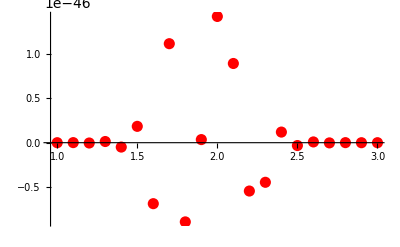

```mathematica
plotwnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

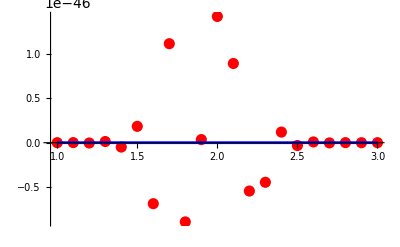

```mathematica
Show[plotwnum,plotwexact]
```

```mathematica
(*check sigma*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/sigma.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,0.},{2.9,-1.74663×10^-19},{2.8,3.56272×10^-19},{2.7,-3.57294×10^-19},{2.6,1.02695×10^-19},{2.5,1.07521×10^-19},{2.4,-9.68269×10^-20},{2.3,-9.17875×10^-20},{2.2,-9.5881×10^-20},{2.1,7.35374×10^-20},{2.,3.4306×10^-19},{1.9,-2.71751×10^-19},{1.8,7.94054×10^-20},{1.7,3.26463×10^-19},{1.6,-6.59511×10^-19},{1.5,3.55588×10^-19},{1.4,9.28611×10^-20},{1.3,-2.14975×10^-19},{1.2,1.82926×10^-19},{1.1,-2.61518×10^-19},{1.,2.82424×10^-19}}

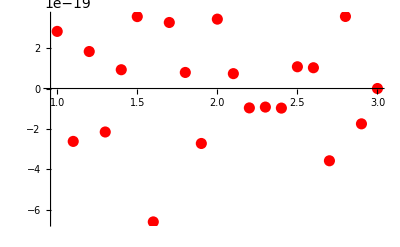

```mathematica
plotσnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

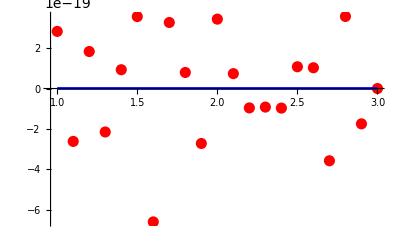

```mathematica
Show[plotσnum,plotσexact]
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.},{2.9,1.98285},{2.8,1.92615},{2.7,1.83062},{2.6,1.69772},{2.5,1.53006},{2.4,1.33179},{2.3,1.10888},{2.2,0.869153},{2.1,0.621944},{2.,0.377289},{1.9,0.144978},{1.8,-0.066345},{1.7,-0.249767},{1.6,-0.400263},{1.5,-0.514516},{1.4,-0.590545},{1.3,-0.627303},{1.2,-0.624365},{1.1,-0.581763},{1.,-0.5}}

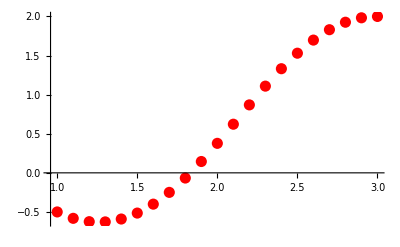

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

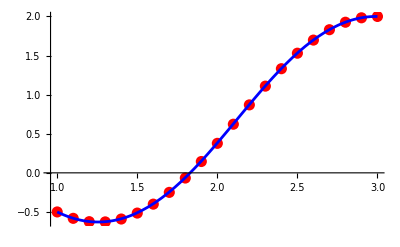

```mathematica
Show[plotψnum,plotψexact]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{1.03452,-0.533813},{1.07613,-0.441782},{1.11431,-0.348283},{1.14525,-0.252164},{1.16502,-0.153163},{1.16971,-0.0523433},{1.15595,0.0476143},{1.12155,0.142443},{1.06628,0.226804},{0.992252,0.29529},{0.90374,0.343622},{0.806281,0.369608},{0.705467,0.373455},{0.605836,0.357405},{0.510242,0.324981},{0.419752,0.280195},{0.333916,0.226995},{0.25121,0.16903},{0.169493,0.109672},{0.0864484,0.0521943},{-6.31269×10^-22,1.35606×10^-20}}

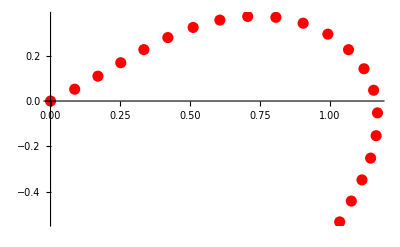

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

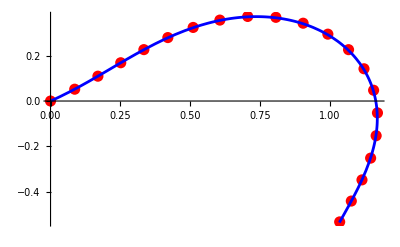

```mathematica
Show[plotXnum,plotXexact]
```